# The Growth of Social Network

```mathematica
a=Import["D:/Mathematica/network5601.txt","Table"];
```

```mathematica
b=Most/@a;
```

```mathematica
c=DeleteDuplicates[Sort/@b];
```

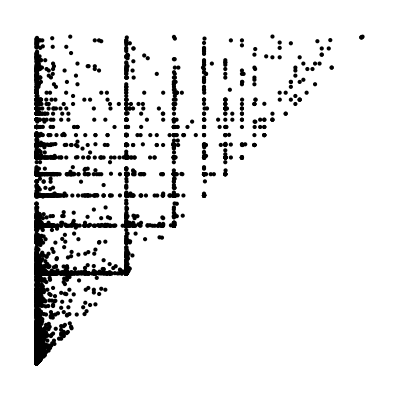

```mathematica
Graphics[{Point[c]}]
```

```mathematica
Manipulate[GraphPlot[Rule@@@Take[c,i],PlotLabel->"Network structure"],{i,1,Length[c],1}]
```

```mathematica
RankPlot[edgelist_]:=Module[{idoccurence,degree,sortdegree},idoccurence=Flatten[edgelist];degree=Transpose[Tally[idoccurence]][[2]];sortdegree=Sort[degree,Greater];ListLogLogPlot[Transpose[{Range[1,Length[sortdegree]],sortdegree}],PlotLabel->"Rank plot of degree distribution (data)",AxesLabel->{"rank","degree"}]];
```

```mathematica
Manipulate[RankPlot[Take[c,i]],{i,1,Length[c],1}]
```